```mathematica
<<KerrQNMs`
<<MaTeX`
```

```mathematica
ω1=KerrQNM[2,2,1];
ω2=KerrQNM[2,2,2];
ω3=KerrQNM[2,2,3];
```

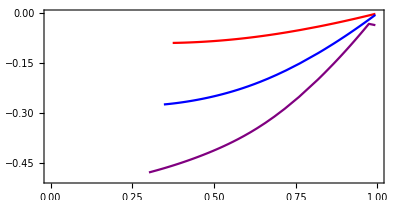

```mathematica
ParametricPlot[{{Re[ω1[a]],Im[ω1[a]]},{Re[ω2[a]],Im[ω2[a]]},{Re[ω3[a]],Im[ω3[a]]}},{a,0,1},PlotRange->{{0,1},{-0.5,0}},Frame->True,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"LM Roman 12",FontSize->12},FrameLabel->{MaTeX["\\rm{Re} (\\omega_n)",Magnification->1.5],MaTeX["\\rm{Im} (\\omega_n)",Magnification->1.5]},PlotLegends->Placed[LineLegend[{MaTeX["n=1",Magnification->1.1],MaTeX["n=2",Magnification->1.1],MaTeX["n=3",Magnification->1.1]},LegendFunction->"Panel"],{0.2,0.6}],PlotStyle->{Red,Blue,Purple}]
```